# Code

```mathematica
computeBisector[pointA_, pointB_]:=Module[{xMid, yMid, m, mInv, b},
(* Provides m, b and an x point of the bisector, given two points *)
xMid=(pointA[[1]]+pointB[[1]])/2;
yMid=(pointA[[2]]+pointB[[2]])/2;
m=(pointA[[2]]-pointB[[2]])/(pointA[[1]]-pointB[[1]]);
mInv=If[m!=0, -1/m, 1000];
b=yMid-mInv*xMid;
(* Returns the slope and the y intercept *)
{mInv, b, pointA[[1]]}
]
```

```mathematica
generateLinesFromPolygon[polygon_]:=Module[{length},
length=Length[polygon];
Append[{polygon[[#]], polygon[[#+1]]}&/@Range[length-1],{ polygon[[length]], polygon[[1]]}]
]
```

```mathematica
doesBisectContainPoint[{m_, b_} , {xP_, yP_}, belowQ_]:=Module[{ yF},
(* Determines if the point on the "right side" of the bisector. *)
yF=m*xP+b;
If[(yF>yP  &&  belowQ) || (yF < yP && Not[belowQ]), True, False]
]
```

```mathematica
determinehowPolyCut[poly_, cutter_, belowQ_]:=Module[{input, cutPolygon={}},
(*  For each point in the polygon, determine if it is contained by the cutter (bisector) *) 
input={#, doesBisectContainPoint[ cutter[[1;;2]],#,  belowQ]}&/@poly;
L=Length[input];
For[i=1, i<=L,
cutPolygon=Append[cutPolygon, {input[[i]], If[i!=L, input[[i+1]], input[[1]]]}];
i++];
(* The output are line segments of the polygon, with each line endpoint of the line segment also labelled by whether the cutter removes it *)
cutPolygon
]
```

```mathematica
lineAbove[{m_, b_},{x_, y_}]:=If[y>m*x+b, False, True]
```

```mathematica
getSlope[{{xa1_, ya1_}, {xa2_, ya2_}}]:=If[xa2-xa1== 0, "undefined",(ya2-ya1)/(xa2-xa1)]
```

```mathematica
getYintercept[{{xa1_, ya1_}, {xa2_, ya2_}}]:=Module[{m},
m=getSlope[ {{xa1, ya1}, {xa2, ya2}}];
 If[m=="undefined", "undefined", ya1-m*xa1] ]
```

```mathematica
intersectPoint[{mA_, bA_, xA_},  {mB_,bB_, xB_}]:=
If[mA==mB, "none",
If[mA=="undefined", If[mB==0, {xA, bB}, {xA, mB*xA+bB}], 
If[mB=="undefined",If[mA==0, {xB, bA},  {xB,mA*xB+bA}],
 {(bB-bA)/(mA-mB), mA*(bB-bA)/(mA-mB)+bA}]]
]
```

```mathematica
processCutPiece[piece_, bisector_]:=Module[{mP, bP, xP, mB, bB, xB, xI, yI },
mP=getSlope[{piece[[1]][[1]], piece[[2]][[1]]}];
bP=getYintercept[{piece[[1]][[1]], piece[[2]][[1]]}];
xP=piece[[1]][[1]][[1]];
mB=bisector[[1]];
bB=bisector[[2]];
xB=bisector[[3]];
{xI, yI}=intersectPoint[{mP, bP, xP},  {mB,bB, xB}];
(* Depending on whether the beginning, end or all of the line segment has been sliced off, provide the appropriate updated line segment *)
If[piece[[1]][[2]] && piece [[2]] [[2]] 
, {piece[[1]][[1]], piece[[2]][[1]]}, 
If[piece[[1]][[2]] && !piece [[2]] [[2]],
 {piece[[1]][[1]],{xI, yI}}, 
If[!piece[[1]][[2]] && piece [[2]] [[2]], 
 {{xI, yI}, piece[[2]][[1]]},
{}]]]
]
```

```mathematica
patchPolygon[polygon_]:=Module[{L=Length[polygon],  newPolygon={}, nextPoint},
For[i=1, i<= L,
nextPoint=If[i==L, 1, i+1];
newPolygon=Append[newPolygon,
 If[polygon[[i]][[2]]!=polygon[[nextPoint]][[1]],
{polygon[[i]], {polygon[[i]][[2]], polygon[[nextPoint]][[1]]}}, 
polygon[[i]]
]];
i++
];
newPolygon]
```

```mathematica
updateVoronoi[cell_, center_, newNeighbor_]:=Module[{bisector, cutPolygon, polyPrePatch, newCell},
bisector=computeBisector[center, newNeighbor];
(* Print[bisector]; First get the bisector determined by the two points *) 
cutPolygon=determinehowPolyCut[cell, bisector, lineAbove[bisector[[1;;2]], center]];
(* Print[cutPolygon]; Now use bisector to label each endpoint of each line in the polygon and whether the bisector slices it off *)polyPrePatch=Partition[Partition[Flatten[processCutPiece[#, bisector]&/@cutPolygon], 2], 2];
(* Generate the final data for the new polygon with line segments updated accoding to which endpoint were sliced off*)
newCell=Partition[Partition[Flatten[patchPolygon[polyPrePatch]], 2], 2];
(* Patch polygon to make sure all endpoints of each segment connect. *)
newCell
]
```

```mathematica
generateWholeCell[originalCell_, center_, points_]:=Module[{i, temp, L=Length[points], steps={}},
temp=updateVoronoi[originalCell, center, points[[1]]];
steps=Append[steps, temp];
For[i=2, i<= L,
temp=updateVoronoi[#[[1]]&/@temp, center, points[[i]]];
steps=Append[steps, temp];
(* Print[{i,temp}]; *)
i++];
{temp, steps}]
```

# Work

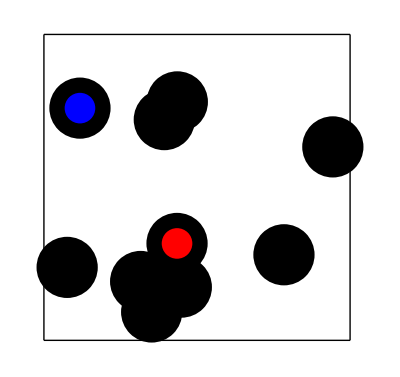

```mathematica
originalCell={{0,0}, {0,1}, {1,1}, {1, 0}};
points ={Random[], Random[]}&/@Range[10];
Graphics[{Line[#]&/@generateLinesFromPolygon[originalCell], Disk[#, 0.1]&/@points, Red, Disk[points[[1]], 0.05],Blue,  Disk[points[[2]], 0.05]}]
```

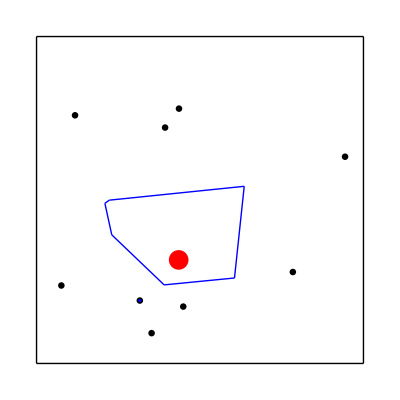

```mathematica
answer=generateWholeCell[originalCell, points[[1]], points[[2;;10]]];
Graphics[{Line[#]&/@generateLinesFromPolygon[originalCell], Disk[#, 0.01]&/@points, Red, Disk[points[[1]], 0.03],Blue,  Line[#]&/@answer[[1]], Disk[points[[5]], 0.005]}]
```